# Convexity of Variance to Entropy

https://twitter.com/nntaleb/status/1209767267111706624

```mathematica
ent1=N[(Sinh[H]+Cosh[H])/(√(2π E))/.H->1]
```

0.657745

```mathematica
ent2=N[(Sinh[H]+Cosh[H])/(√(2π E))/.H->2]
```

1.78794

```mathematica
entX=RandomVariate[NormalDistribution[0,ent1],10^4];
```

```mathematica
entY=RandomVariate[NormalDistribution[0,ent2],10^4];
```

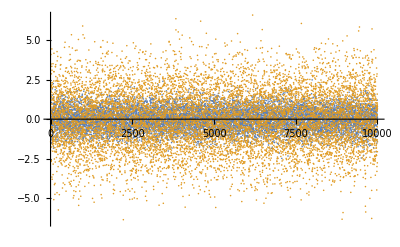

```mathematica
ListPlot[{entX,entY},PlotRange->{-6.5,6.5}]
```

```mathematica
varX=RandomVariate[NormalDistribution[0,ent1],10^4];
```

```mathematica
varY=RandomVariate[NormalDistribution[0,√2*ent1],10^4];
```

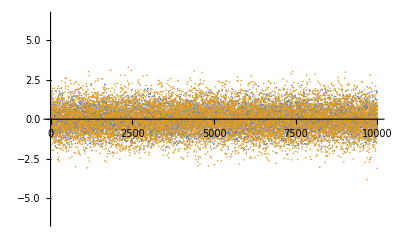

```mathematica
ListPlot[{varX,varY},PlotRange->{-6.5,6.5}]
```